```mathematica
rollRate[t_,a_,v0_]:=a*t+v0
roll[t_,a_,v0_,r0_] := a*t^2/2+v0*t+ r0
PIDStep[Prop_,Int_,Deriv_][{SP_,PV_,e0_,ii0_},dt_]:=Prop*(SP-PV)+Int*(ii0+dt*(SP-PV))+Deriv*(SP-PV - e0)/dt
```

```mathematica
RollPIDStep[Prop_,Int_,Deriv_,dt_][{tau0_,v0_,r0_,e0_,ii0_}]:={
PIDStep[Prop,Int,Deriv][{roll[dt,tau0,v0,r0],r0,e0,ii0},dt],
rollRate[dt,tau0,v0],
roll[dt,tau0,v0,r0],
roll[dt,tau0,v0,r0]-r0,
ii0+dt*(roll[dt,tau0,v0,r0]-r0)
}
```

```mathematica
RollPIDEvol[dt_,n_][Prop_,Int_,Deriv_][tau0_,v0_,r0_]:=NestList[RollPIDStep[Prop,Int,Deriv,dt],{tau0,v0,r0,0,0},n]
```

```mathematica
data[dt_,T_,i_][Prop_,Int_,Deriv_][tau0_,v0_,r0_]:=Transpose@{NestList[#1+dt &,0,Abs[IntegerPart[T/dt]]],#1[[i]]&/@RollPIDEvol[dt,Abs[IntegerPart[T/dt]]][Prop,Int,Deriv][tau0,v0,r0]}
```

```mathematica
(* PlotRange->All, Filling->Axis *)
```

```mathematica
RollPIDPlot[dt_,T_,i_][Prop_,Int_,Deriv_][tau0_,v0_,r0_]:= ListPlot[
Legended[
data[dt,T,i][Prop,Int,Deriv][tau0,v0,r0],
"Proportional="<>ToString[Prop]<>"\nIntegral="<>ToString[Int]<>"\nDerivative="<>ToString[Deriv]
],PlotLabel->If[i==1,"Torque:",If[i==2,"Roll rate:",If[i==3,"Roll:","Unknown:"]]]<>" tau0="<>ToString[tau0]<>" & v0="<>ToString[v0]<>" & r0="<>ToString[r0]]
```

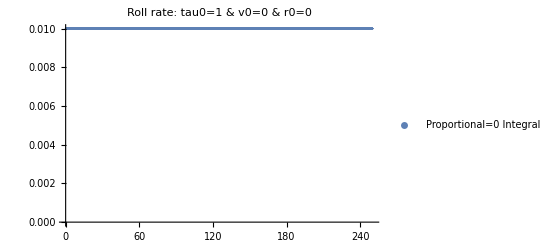

```mathematica
RollPIDPlot[0.01,250,2][0,0,0][1,0,0]
```

```mathematica
(* Observation: Proportional > 0 ==> Diverges *)
```

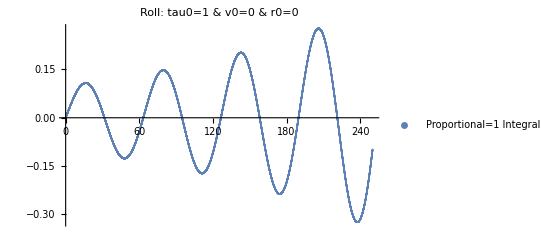

```mathematica
RollPIDPlot[0.01,250,3][1,-1,-1][1,0,0]
```

```mathematica
(* Observation: Proportional = 0 ==> Oscillates *)
```

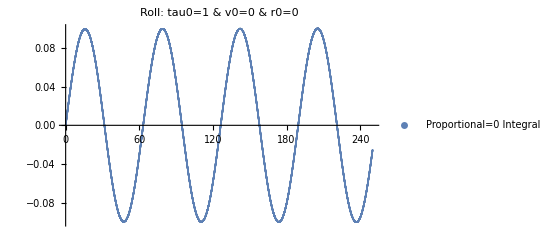

```mathematica
RollPIDPlot[0.01,250,3][0,-1,-1][1,0,0]
```

```mathematica
(* Observation: Integral >= 0 ==> Increases *)
```

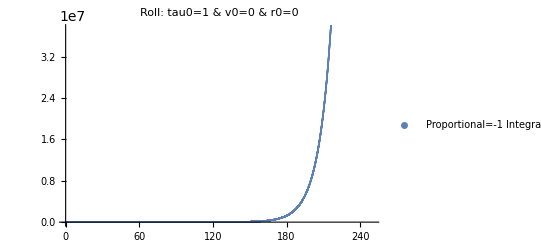

```mathematica
RollPIDPlot[0.01,250,3][-1,1,-1][1,0,0]
```

```mathematica
(* Observation: Higher values of derivative slowly increase the frecuency *)
```

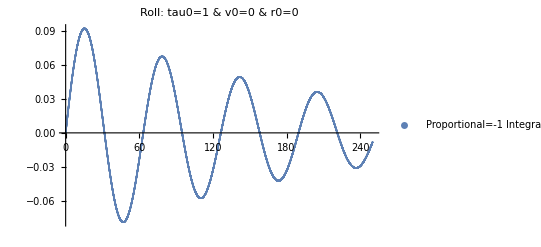

```mathematica
RollPIDPlot[0.01,250,3][-1,-1,-1][1,0,0]
```

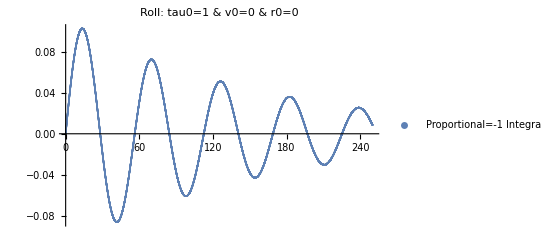

```mathematica
RollPIDPlot[0.01,250,3][-1,-1,20][1,0,0]
```

```mathematica
Clear["Global`*"]
```